#### Finding Tangent and Normal to a Curve Input Curve r as a vector {x(t),y(t)} with the parametric variable

```mathematica
ClearAll["Global`*"]

r[t_]:= {Cos[2*Pi*t],1/2*t}
```

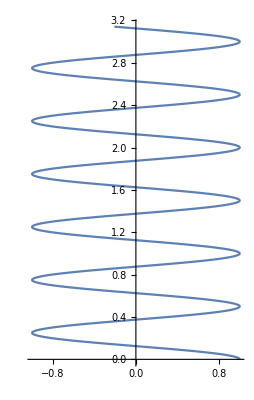

```mathematica
ParametricPlot[r[t],{t,0,2*Pi}]
```

```mathematica
sols = FrenetSerretSystem[ {x[t],y[t]}, t] // Last // Simplify 
Print["Unit Tangent ="];
unitTan = sols[[1]]

Print["Unit Normal ="];
unitNorm = sols[[2]]
```

{{x'[t]/(√(x'[t]^2+y'[t]^2)),y'[t]/(√(x'[t]^2+y'[t]^2))},{-y'[t]/(√(x'[t]^2+y'[t]^2)),x'[t]/(√(x'[t]^2+y'[t]^2))}}

Unit Tangent =

{x'[t]/(√(x'[t]^2+y'[t]^2)),y'[t]/(√(x'[t]^2+y'[t]^2))}

Unit Normal =

{-y'[t]/(√(x'[t]^2+y'[t]^2)),x'[t]/(√(x'[t]^2+y'[t]^2))}

{{1/(√(1+4 π^2 Sin[2 π t]^2)),-(2 π Sin[2 π t])/(√(1+4 π^2 Sin[2 π t]^2))},{(2 π Sin[2 π t])/(√(1+4 π^2 Sin[2 π t]^2)),1/(√(1+4 π^2 Sin[2 π t]^2))}}

```mathematica
sols = FrenetSerretSystem[ r[t], t] // Last // Simplify
```

{{-(4 π Sin[2 π t])/(√(1+16 π^2 Sin[2 π t]^2)),1/(√(1+16 π^2 Sin[2 π t]^2))},{-1/(√(1+16 π^2 Sin[2 π t]^2)),-(4 π Sin[2 π t])/(√(1+16 π^2 Sin[2 π t]^2))}}